```mathematica
outcomepoints := {{0,1}, {1,0}, {0,0}}
outcomepoints3d := {{1,0,0}, {0,1,0}, {0,0,0}, {0,0,1}}

L[r_, y_] := Norm[r-y,2]^2


exL[r_, p_] := Sum[p[[i]] L[r, outcomepoints[[i]]], {i,1,3}]
exL3D[r_, p_] := Sum[p[[i]] L[r, outcomepoints3d[[i]]], {i,1,4}]
(*min[p_] := Last[Minimize[exL[{r1, r2}, p],{r1,r2}]]
gamma[p_] := {r1 /. min[p], r2 /. min[p]}*)
gamma[p_] := ArgMin[exL[{r1, r2}, p], {r1, r2}]
gamma3d[p_] := ArgMin[exL3D[{r1, r2,r3}, p], {r1, r2, r3}]
```

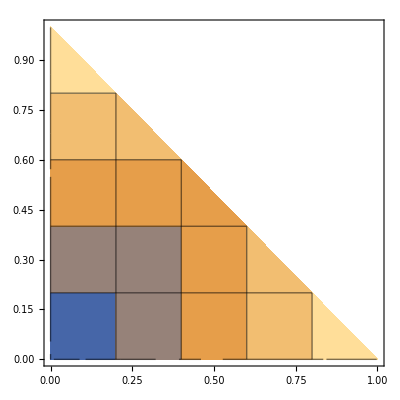
{140.484,-Graphics-}

{879.724,-Graphics3D-}

```mathematica
Timing[ContourPlot[gamma[{p1, p2, 1-p1-p2}]  , {p1, 0, 1}, {p2, 0 ,1}, PerformanceGoal->"Speed", RegionFunction-> Function[{p1, p2}, p1 + p2 ≤ 1  ]] ]
Timing[ContourPlot3D[gamma3d[{p1, p2, p3, 1-p1-p2-p3}]  , {p1, 0, 1}, {p2, 0 ,1}, {p3,0,1},Contours->3, PerformanceGoal->"Speed", RegionFunction-> Function[{p1, p2, p3}, p1 + p2 +p3 ≤ 1  ]] ]
(*Timing[RegionPlot[gamma[{p1, p2, 1-p1-p2}]  ≤ {0.01, 0.01}, {p1, 0, 1}, {p2, 0 ,1}, PerformanceGoal->"Speed" ] ]*)

(*BR[p_] :=First[-Minimize[exL[{r1, r2}, p],{r1,r2}]]*)

(*ptgen[p1_, p2_] := {p1, p2, BR[{p1, p2, 1-p1-p2}]}
points := Table[ptgen[p1, p2], {p1, 0, 1, 0.1}, {p2, 0,1,0.1}]
pts :=Flatten[points, 1]*)

(*ListPlot3D[pts, InterpolationOrder -> 1, ColorFunction->Hue, RegionFunction->Function[{p1, p2}, p1 + p2 ≤ 1  ]]
ListPlot3D[pts, InterpolationOrder -> 2, ColorFunction->Hue, RegionFunction->Function[{p1, p2}, p1 + p2 ≤ 1  ]]*)
```

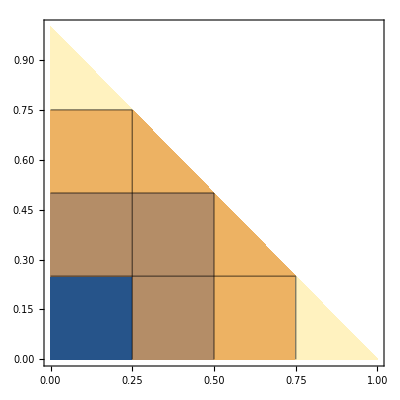
{94.548,-Graphics-}

```mathematica
"2-norm squared"
```

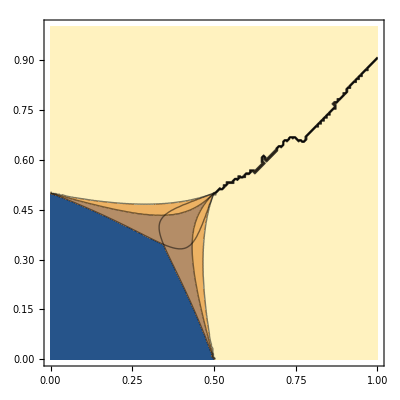
```mathematica
"2 norm"
{892.108,-Graphics-}
```

```mathematica
(*simplex := Graphics3D[{Opacity[0.1],Simplex[{{0,0,1},{1,0,0},{0,1,0},{0,0,0}}]}]*)
plotBR := ContourPlot[BR[{p1, p2, 1-p1-p2}] == 0.5, {p1, 0, 1},{p2, 0, 1}, RegionFunction->Function[{p1, p2}, p1 + p2 ≤ 1  ], Axes -> False ]
plotBR
```

```mathematica
"END 3 OUTCOMES"
```

```mathematica
outcomes := {0,1,2,3}
outcomepoints = {{0,0,0}, {1,0,0}, {0,1,0}, (0,0,1)}
L[r_, y_] := Norm[r-y, 2]
exL[r_, p_] := Sum[p[[i]] L[r, outcomepoints[[i]]], {i,1,4}]
BR[p_] := First[-Minimize[exL[r, p],r]]
min[p_] := Last[Minimize[exL[r, p],r]]
gamma[p_] := {}
```

```mathematica
ContourPlot3D[BR[{x,y,z, 1-x-y-z}] , {x,0,1}, {y,0,1}, {z,0,1} , Contours->5]
```

-Graphics3D-

```mathematica
(*NOTE: p1 = {0,0,1}, p2 = {1,0,0}, p3 = {0,1,0}, p4 = {0,0,0}*)
outcomepoints := {{0,0,1}, {1,0,0}, {0,1,0}, {0,0,0}}
L[r_, y_] := Norm[r-y, 2]

exL[r_, p_] := Sum[p[[i]] L[r, outcomepoints[[i]]], {i,1,4}]
BR[p_] := First[-Minimize[exL[{r1, r2, r3}, p],{r1,r2, r3}]]
BR[{1,0,0, 0}]

(*simplex := Graphics3D[{Opacity[0.1],Simplex[{{0,0,1},{1,0,0},{0,1,0},{0,0,0}}]}]*)
plotBR3D := ContourPlot3D[BR[{p1, p2, p3, 1-p1-p2-p3}], {p1, 0, 1},{p2, 0, 1},{p3, 0, 1}, RegionFunction->Function[{p1, p2, p3}, p1 + p2 + p3 ≤ 1  ], Axes -> False ]
```

```mathematica
Show[simplex]
```

```mathematica
(*binary1 := ContourPlot3D[p1 ==  0.5, {p1, 0,1},{p2, 0,1},{p3, 0, 1}, RegionFunction->Function[{p1, p2, p3}, p1 + p2 + p3 ≤ 1], Axes -> False]
binary2 := ContourPlot3D[p2 == p3, {p1, 0,1},{p2, 0,1},{p3, 0, 1}, RegionFunction->Function[{p1, p2, p3}, p1 + p2 + p3 ≤ 1], Axes-> False]
binaryprops := {binary1, binary2}*)


(*mode1 := ContourPlot3D[p1 == Max[p1, p2, p3, 1-p1-p2-p3], {p1, 0,1},{p2, 0,1},{p3, 0, 1}, RegionFunction->Function[{p1, p2, p3}, p1 + p2 + p3 ≤ 1 ], Axes -> False]
mode2 := ContourPlot3D[p2 == Max[p1, p2, p3, 1-p1-p2-p3], {p1, 0,1},{p2, 0,1},{p3, 0, 1}, RegionFunction->Function[{p1, p2, p3}, p1 + p2 + p3 ≤ 1 ], Axes -> False]
mode3 := ContourPlot3D[p3 == Max[p1, p2, p3, 1-p1- p2-p3], {p1, 0,1},{p2, 0,1},{p3, 0, 1}, RegionFunction->Function[{p1, p2, p3}, p1 + p2 + p3 ≤ 1 ], Axes -> False]
modeprops := {mode1, mode2, mode3}*)

(*alpha := 0.5
absmode1 := ContourPlot3D[p1 ==alpha, {p1, 0,1},{p2, 0,1},{p3, 0, 1}, RegionFunction->Function[{p1, p2, p3}, p1 + p2 + p3 ≤ 1  ], Axes -> False]
absmode2 := ContourPlot3D[p2 == alpha, {p1, 0,1},{p2, 0,1},{p3, 0, 1}, RegionFunction->Function[{p1, p2, p3}, p1 + p2 + p3 ≤ 1  ], Axes -> False]
absmode3 := ContourPlot3D[p3 == alpha, {p1, 0,1},{p2, 0,1},{p3, 0, 1}, RegionFunction->Function[{p1, p2, p3}, p1 + p2 + p3 ≤ 1  ], Axes -> False]
absmode4 := ContourPlot3D[1-p1-p2-p3 == alpha, {p1, 0,1},{p2, 0,1},{p3, 0, 1}, RegionFunction->Function[{p1, p2, p3}, p1 + p2 + p3 ≤ 1  ], Axes -> False]
absmodeprops := {absmode1, absmode2, absmode3, absmode4}*)

(*modalmass[r_] := ContourPlot3D[r == Max[p1, p2, p3, 1-p1-p2-p3], {p1, 0,1},{p2, 0,1},{p3, 0, 1}, RegionFunction->Function[{p1, p2, p3}, p1 + p2 + p3 ≤ 1 ], Axes -> False]

modalprops := {modalmass[0.5]}*)
```

```mathematica
geomed[r_] := ContourPlot3D[r /.Last[Maximize[Norm[z - {p1, p2, p3, 1-p1-p2-p3}], r]], {p1, 0,1},{p2, 0,1},{p3, 0, 1}, RegionFunction->Function[{p1, p2, p3}, p1 + p2 + p3 ≤ 1 ], Axes -> False]
geomedprops := {geomed[{0.5, 0.2, 0.3, 0}]}

(*binaryplt =Show[binaryprops,simplex, Axes-> False , Boxed -> False]
modeplt =Show[modeprops,simplex, Axes-> False , Boxed -> False]*)
(*absmodeplt =Show[absmodeprops,simplex, Axes-> False , Boxed -> False]*)
(*mmplt =Show[modalprops,simplex, Axes-> False , Boxed -> False]*)
geomedplt = Show[geomedprops, Axes-> False , Boxed -> False]
```

1/4

{(√3)/2,{r→1/4}}

{-1+r,r,r,r}

Maximize::ivar: 0.5 is not a valid variable.

ReplaceAll::reps: {0.5,0.2,0.3,0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Maximize::ivar: 0.5 is not a valid variable.

ReplaceAll::reps: {0.5,0.2,0.3,0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Maximize::ivar: 0.5 is not a valid variable.

General::stop: Further output of Maximize::ivar will be suppressed during this calculation.

ReplaceAll::reps: {0.5,0.2,0.3,0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ContourPlot3D[{0.5,0.2,0.3,0}/.Last[Maximize[Norm[Plus[«2»]],{0.5,0.2,0.3,0}]],{p1,0,1},{p2,0,1},{p3,0,1},RegionFunction→Function[{p1,p2,p3},p1+p2+p3≤1],Axes→False]},Axes→False,Boxed→False].

Show[{ContourPlot3D[{0.5,0.2,0.3,0}/.Last[Maximize[Norm[z-{p1,p2,p3,1-p1-p2-p3}],{0.5,0.2,0.3,0}]],{p1,0,1},{p2,0,1},{p3,0,1},RegionFunction→Function[{p1,p2,p3},p1+p2+p3≤1],Axes→False]},Axes→False,Boxed→False]

```mathematica
outcomepoints := {{0,0,1}, {0, 1,0}, {0,0,0}, {1,0,0}}
L[r_, y_] := Norm[r-y, 2]

exL[r_, p_] := Sum[p[[i]] L[r, outcomepoints[[i]] ], {i,1,4}]
BR[p_] :=First[-Minimize[exL[{r1, r2,r3}, p],{r1,r2,r3}]]

ptgen[p1_, p2_, p3_] := {p1, p2, p3, BR[{p1, p2,p3, 1-p1-p2-p3}]}
pts := Flatten[Table[ptgen[p1, p2, p3], {p1, 0, 1, 0.05}, {p2, 0,1,0.05}, {p3, 0, 1, 0.05}],2]
pts
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize::cvmit will be suppressed during this calculation.

$Aborted

```mathematica
ListContourPlot3D[pts, Contours-> {0.5}, ColorFunction->Hue, RegionFunction->Function[{p1, p2, p3}, p1 + p2 + p3 ≤ 1  ]]
```

-Graphics3D-